```mathematica
Clear["Global`*"]
```

```mathematica
(* g is an increasing function of z. *)
cond1=g*(2-Qdg)-1;
eq1=Collect[Simplify[(1-z)*gy+z*gz-g/.{gy->Qdg*g+1-g,gz->Qcg*g2+Qdg(g-g2)+1-g}],g2];
eq2=Collect[Simplify[z(1-z)*gy^2+(g-(1-z)*gy)^2-z*g2/.{gy->Qdg*g+1-g}],g2];
M1=-2 (-2+g (-3+Qdg) (-1+Qdg)+Qdg) z;
M2=2 (1+g (-2+Qdg))(-2+Qdg) ;
M3=(-2+Qdg);
h=eq1/.{g2*z->eq2+z*g2}
{k0,k1}=FullSimplify[CoefficientList[D[h/.{g->g[z]},z],g'[z]]/.{g[z]->g}]
```

1+g (-2+Qdg)+(Qcg-Qdg) ((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z)

{(1+g (-3+Qdg)) (1+g (-1+Qdg)) (-Qcg+Qdg),(-2+Qdg) (1+2 Qcg (1+g (-2+Qdg))-2 (Qdg+g (-2+Qdg) Qdg))+2 (-Qcg+Qdg) (-2+g (-3+Qdg) (-1+Qdg)+Qdg) z}

```mathematica
Collect[Expand[h],Qcg]
```

1-2 g-Qdg+5 g Qdg-4 g^2 Qdg-2 g Qdg^2+4 g^2 Qdg^2-g^2 Qdg^3+Qdg z-4 g Qdg z+3 g^2 Qdg z+2 g Qdg^2 z-4 g^2 Qdg^2 z+g^2 Qdg^3 z+Qcg (1-4 g+4 g^2+2 g Qdg-4 g^2 Qdg+g^2 Qdg^2-z+4 g z-3 g^2 z-2 g Qdg z+4 g^2 Qdg z-g^2 Qdg^2 z)

```mathematica
FullSimplify[1-4 g+4 g^2+2 g Qdg-4 g^2 Qdg+g^2 Qdg^2-z+4 g z-3 g^2 z-2 g Qdg z+4 g^2 Qdg z-g^2 Qdg^2 z-k1]
```

3+4 Qcg-5 Qdg+g^2 (4-(-4+Qdg) Qdg (-1+z)-3 z)+2 (Qcg-Qdg) (Qdg (-1+z)-2 z)-z+2 g ((-Qcg (-2+Qdg)+(-1+Qdg)^2) (-2+Qdg)+(2+Qcg (-3+Qdg) (-1+Qdg)-(-2+Qdg)^2 Qdg) z)

```mathematica
Collect[k1-h,Qcg]
```

-3-g (-2+Qdg)+Qdg-2 (-2+Qdg) (Qdg+g (-2+Qdg) Qdg)+2 Qdg (-2+g (-3+Qdg) (-1+Qdg)+Qdg) z+Qdg ((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z)+Qcg (2 (1+g (-2+Qdg)) (-2+Qdg)-(g+(1+g (-1+Qdg)) (-1+z))^2-2 (-2+g (-3+Qdg) (-1+Qdg)+Qdg) z+(1+g (-1+Qdg))^2 (-1+z) z)

```mathematica
1-4 g+4 g^2+2 g Qdg-4 g^2 Qdg+g^2 Qdg^2-z+4 g z-3 g^2 z-2 g Qdg z+4 g^2 Qdg z-g^2 Qdg^2 z
```

1-4 g+4 g^2+2 (1+g (-2+Qdg)) (-2+Qdg)+2 g Qdg-4 g^2 Qdg+g^2 Qdg^2-z+4 g z-3 g^2 z-2 g Qdg z+4 g^2 Qdg z-g^2 Qdg^2 z-2 (-2+g (-3+Qdg) (-1+Qdg)+Qdg) z

```mathematica
Expand[M1+M2]
```

1/2 (-4+8 g+2 Qdg-8 g Qdg+2 g Qdg^2+4 z-6 g z-2 Qdg z+8 g Qdg z-2 g Qdg^2 z)

```mathematica
Expand[4-(-4+Qdg) Qdg (-1+z)-3 z]
```

4-4 Qdg+Qdg^2-3 z+4 Qdg z-Qdg^2 z

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qdg)≥ 1&&1>Qcg>Qdg>0&&h==0&&1≥z≥0,FullSimplify@Reduce[(M1+M2)*(Qcg-Qdg)<  -M3]]
```

True

```mathematica
FullSimplify[(M1+M2)*(Qcg-Qdg)-h]
```

-1-g (-2+Qdg)+(Qcg-Qdg) (2 g (4-(-4+Qdg) Qdg (-1+z)-3 z)-2 (-2+Qdg) (-1+z))-(Qcg-Qdg) ((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z)

```mathematica
FullSimplify[(M1+M2)*(Qcg-Qdg)+h]
```

1+g (-2+Qdg)+(Qcg-Qdg) (2 g (4-(-4+Qdg) Qdg (-1+z)-3 z)-2 (-2+Qdg) (-1+z))+(Qcg-Qdg) ((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z)

```mathematica
Simplify[(M1+M2)*(Qcg-Qdg)+M3-k1]
```

0

```mathematica
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
```

```mathematica
Together[Qcg*g+1-g]
```

(-e+e^2+2 e g-3 e^2 g-2 e g^2+3 e^2 g^2+e g^3-e^2 g^3-g ϵ+2 e g ϵ+g^2 ϵ-2 e g^2 ϵ-g^3 ϵ+g^3 ϵ^2)/((-e+e g-g ϵ) (1-e+e g-g ϵ))

```mathematica
numdomzx=NumeratorDenominator[Together[Qcg*g+1-g]];
polyzx = Assuming[r>1&&1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Sign[numdomzx[[2]]]]*numdomzx[[1]];
{a0,a1,a2,a3}=Simplify[CoefficientList[polyzx/.{g->g+1},g]];
```

```mathematica
Assuming[r>1&&1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0,FullSimplify@Reduce[a0>0]]
Assuming[r>1&&1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0,FullSimplify@Reduce[a1>0]]
Assuming[r>1&&1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0,FullSimplify@Reduce[a2>0]]
Assuming[r>1&&1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0,FullSimplify@Reduce[a3>0]]
```

True

2 (1+e) ϵ>e+3 ϵ^2

2 (1+e) ϵ>e+3 ϵ^2

True

```mathematica
polyzx
```

e-e^2-2 e g+3 e^2 g+2 e g^2-3 e^2 g^2-e g^3+e^2 g^3+g ϵ-2 e g ϵ-g^2 ϵ+2 e g^2 ϵ+g^3 ϵ-g^3 ϵ^2

```mathematica
numdomgx=NumeratorDenominator[Together[Qcg*g+1-g]];
numdomgy=NumeratorDenominator[Together[Qdg*g+1-g]];
numdomgz=NumeratorDenominator[Together[Qdg*g+1-g]];
polygx = Assuming[r>1&&1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Sign[numdomgx[[2]]]]*numdomgx[[1]];
polygy = Assuming[r>1&&1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Sign[numdomgy[[2]]]]*numdomgy[[1]];
{a0,a1,a2,a3}=Simplify[CoefficientList[polyzx/.{g->g+1},g]];
polygz = Assuming[r>1&&1>e1>0&&ϵ==(1-e1)*(1-e)+e1*e&&1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Sign[numdomgz[[2]]]]*numdomgz[[1]];
{a0,a1,a2,a3}=Simplify[CoefficientList[polyzx/.{g->g+1},g]];
```

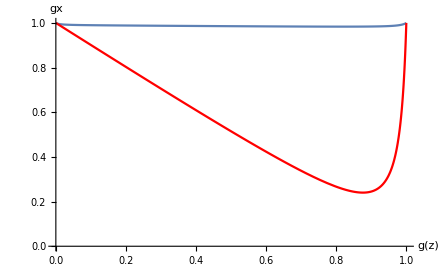

```mathematica
Show[{Plot[Evaluate[Qcg*g+1-g//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g(z)","gx"},PlotRange->{0,1}],
Plot[Evaluate[Qdg*g+1-g//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g(z)","gy"},PlotStyle->Red,PlotRange->{0,1}]}]
```

```mathematica
Collect[g-z*(g2*(Qcg-Qdg)+Qdg*g+1-g)-(1-z)*(Qcg*g+1-g),z]
```

-1+2 g-g Qcg+(g Qcg-g2 (Qcg-Qdg)-g Qdg) z

```mathematica
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
```

```mathematica
FullSimplify[D[Qdg,g]]
```

((-1+e)^2 e^2 (-1+g)^2+e g (2-2 g+e (-2+3 g)) ϵ+g (e (-2+e (2-3 g))+g) ϵ^2+(-1+2 e) g^2 ϵ^3)/((-1+e-e g+g ϵ)^2 (e-e g+g ϵ)^2)

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1>g>0&&1>Qcg>0,FullSimplify@Reduce[D[Qcg*g,g]>1]]
```

$Aborted

```mathematica
sol=(-1+e)^2 e^2 (-1+g)^2+e g (2-2 g+e (-2+3 g)) ϵ+g (e (-2+e (2-3 g))+g) ϵ^2+(-1+2 e) g^2 ϵ^3-(-1+e-e g+g ϵ)^2 (e-e g+g ϵ)^2
```

```mathematica
FullSimplify[(-1+e)^2 e^2 (-1+g)^2+e g (2-2 g+e (-2+3 g)) ϵ+g (e (-2+e (2-3 g))+g) ϵ^2+(-1+2 e) g^2 ϵ^3-(-1+e-e g+g ϵ)^2 (e-e g+g ϵ)^2]
```

-g (e-ϵ)^2 (e^2 (-2+g) (-1+g)^2-2 e (-1+g)^2 (-1+g ϵ)+g ϵ (1+g (-2+g ϵ)))

```mathematica
e^2 (-2+g) (-1+g)^2-2 e (-1+g)^2 (-1+g ϵ)+g ϵ (1+g (-2+g ϵ))
```

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1>g>0&&1>Qcg>0,FullSimplify@Reduce[e^2 (-2+g) (-1+g)^2-2 e (-1+g)^2 (-1+g ϵ)+g ϵ (1+g (-2+g ϵ))<0]]
```

$Aborted